## Preamble

## Properties of Complex Numbers

### 0.) Preamble

```mathematica
z=1/2+1/2 √3 I;
w=-1/2+1/2 √3 I;
con=3;
w^6//Expand;
```

### 1)

```mathematica
Abs[z];
Abs[w];
Abs[z w];
Abs[z w]===Abs[z]Abs[w]
```

True

### 2)

```mathematica
Abs[w];
Abs[con w];
con Abs[w];
Abs[con w]===con Abs[w]
```

True

### demo)

```mathematica
Abs[ww]"1)"//TraditionalForm
"1)   "  Abs[ww]//TraditionalForm
```

1) Abs[ww]

1)    Abs[ww]

## Triangle Inequality Theorem

```mathematica
Abs[z+w]<=Abs[z]+Abs[w]
```

True

## Cauchy Riemann Equations

```mathematica
f[z_]:=z^3-z^2
ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}
```

-x^2+x^3+y^2-3 x y^2+ⅈ (-2 x y+3 x^2 y-y^3)

```mathematica
Refine[Re[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}]
Refine[Im[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}]
```

-x^2+x^3+y^2-3 x y^2

-2 x y+3 x^2 y-y^3

```mathematica
D[Refine[Re[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],x]
D[Refine[Im[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],y]

D[Refine[Re[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],y]
-D[Refine[Im[ComplexExpand[f[z],z]/.{Re[z]:>x,Im[z]:>y}],{Element[x,Reals],Element[y,Reals]}],x]
```

-2 x+3 x^2-3 y^2

-2 x+3 x^2-3 y^2

2 y-6 x y

2 y-6 x y

## Length of a path

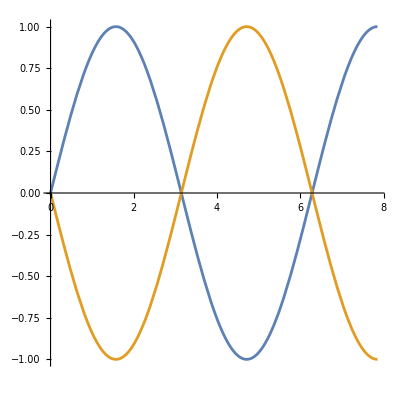

```mathematica
f[x_]:=Sin[x]
Plot[{f[x],Cos[x+Pi/2]},{x,0,2.5Pi},AspectRatio->1]
```

```mathematica
f'[t];
Integrate[√(1+f'[t]^2),{t,0,2Pi}];
Table[Integrate[√(1+Cos'[t-Pi/2]^2),{t,k/2 Pi,2Pi+k/2 Pi}],{k,0,2}]//TableForm
```

4 √2 EllipticE[1/2]
4 √2 EllipticE[1/2]
4 √2 EllipticE[1/2]

## tmp. notes

```mathematica
ContourIntegrate[z^2,z∈Line[{{0,0},{1,1}}]]
```

-2/3+(2 ⅈ)/3

```mathematica
(1+I)^3/3//Simplify
```

-2/3+(2 ⅈ)/3

```mathematica
ContourIntegrate[z^2,z∈Line[{{0,0},{0,1},{1,0},{1,1}}]]
```

-2/3+(2 ⅈ)/3

```mathematica
CoordinateTransform["Polar"->"Cartesian",{r,θ}]
CoordinateTransform["Cartesian"-> "Polar",{x,y}]
CoordinateTransform["Cartesian"-> "Spherical",{x,y,0}]
```

{r Cos[θ],r Sin[θ]}

{√(x^2+y^2),ArcTan[x,y]}

{√(x^2+y^2),ArcTan[0,√(x^2+y^2)],ArcTan[x,y]}

```mathematica
Conjugate[2+3I]
```

2-3 ⅈ

```mathematica
z=1+2I;
w=-1+√I;
Abs[z]Abs[w]//Simplify
Abs[z w]//Simplify
√3 Abs[z]
Abs[√3 z]
z/Abs[z]//Abs
w/Abs[w]//Abs
```

√(10-5 √2)

√(10-5 √2)

√15

√15

1

1

```mathematica
z/Abs[z]
Abs[z/Abs[z]]
```

(1+2 ⅈ)/(√5)

1

```mathematica
z Conjugate[z]
```

5

```mathematica
Abs[z]
Abs[Conjugate[z]]
```

1

1

```mathematica
ClearAll[w,z]
```

```mathematica
z
```

z

```mathematica
w
```

w

```mathematica
Import["http://www.mathematicaguidebooks.org/V6/downloads/RiemannSurfacePlot3D.m"]
```

```mathematica
rsurf[func_]:=Grid[{{RiemannSurfacePlot3D[w==func,Re[w],{z,w},ImageSize->400,Coloring->Hue[Rescale[ArcTan[1.4 Im[w]],{-Pi/2,Pi/2}]],PlotPoints->{40,40},Boxed->False],RiemannSurfacePlot3D[w==func,Im[w],{z,w},ImageSize->400,Coloring->Hue[Rescale[ArcTan[1.4 Re[w]],{-Pi/2,Pi/2}]],PlotPoints->{40,40},Boxed->False]}}];
```

```mathematica
rsurf[Log[z]]
```

-Graphics3D- | -Graphics3D-

```mathematica
Import["http://www.mathematicaguidebooks.org/V6/downloads/RiemannSurfacePlot3D.m",{"Text","Lines"}]
```

{(* ::Package:: *),,(* ::Subtitle:: *),(*Plotting Riemann Surfaces of Compositions of Elementary Functions*),,,(* ::Subsection::Closed:: *),(*Version information*),,,(* ::Text:: *),(*Author:  Michael Trott (mtrott@wolfram.com)*),(**),(*Version:  2.0.42 (June 2007)*),(**),(*Tested Mathematica Version:  6.0*),(**),(*From: The Mathematica GuideBook for Numerics, second edition, Springer 2008*),(**),(*Copyright:  Springer 2008*),(**),(*Limitations: *),(*- Only functions with finitely many branch points, all of which can be determined in closed form, can be plotted.*),,,(* ::Subsection::Closed:: *),(*Outline of the algorithm*),,,(* ::Text:: *),(*To construct the Riemann surface we will proceed with the following, partially symbolic, partially numerical steps:*),(**),(*We assume given an equation of the form w = w(z) (or f(w, z) = c and we assume that we can solve for w=w(z)). *),(*We consider the functions of the form w(z) = q(z) where q(z) is a composition of nested elementary functions, including root objects. *),(*We will display Riemann surfaces of the form Re(w(z)) and Im(w(z)).*),(*After having checked that we can deal with the function at hand, the following steps are carried out:*),(**),(*1. *),(*All branch points come from either due to arctrig functions, logarithms, radicals, or roots. For a uniform treatment, we transform all arctrig functions into a representation using only logarithms. We then extract all log\[Dash]terms and radicals and root\[Dash]objects and determine their branchpoints independently. These are the (potential) branchpoints of the function under consideration. Determining the location branch points will be done using Reduce and we consider only the case were we have finitely many branch points that can be expressed in closed form.*),(**),(*2. *),(*Then, we divide the complex z\[Dash]plane radially and azimuthally into sectors generated by the outer product of the radial and azimuthal coordinates of the branch points, so that every sector has no interior branch points.*),(**),(*3. *),(*We generate some possible sheets of the function. For radicals and Root\[Dash]objects we generate all possible sheets, and for logarithmic terms we use n (by default we will use three sheets) out of the infinitely many sheets.*),(**),(*4. *),(*We derive a set of coupled nonlinear ordinary differential equations describing w_j(z) as a rational function in z and the w_k(z) for all radical and logarithmic expressions. Solving such a system of differential equation with branch-cut free right-hand sides avoids meeting branch cuts.*),(**),(*5. *),(*By starting quite near the branch points, we solve the differential equation radially outwards for all sheets of every sector. Here it is important to avoid calculating sheets more than once.*),(**),(*6. *),(*Starting from the radial solutions of the differential equations constructed in step 3) we solve the differential equation azimuthally inside the sectors constructed in step 2). These solutions results in parametrized (parametrized by the radius r and the angle \[CurlyPhi]) parts of all sheets for each sector.*),(**),(*7. *),(*We generate values and derivatives of all patches for all sheets. Potentially, interpolate the values.*),(**),(*8.  *),(*We form graphics complexes of polygons with normals for all patches of all sheets and apply potential plot styles, color functions and form the resulting 3D graphics object. Potentially small graphics complexes that stitch the graphics complexes of the patches over the sectors are added. *),,,(* ::Subsection::Closed:: *),(*Package context change*),,,BeginPackage["RiemannSurfacePlot3D`"] ,,,(* ::Subsection::Closed:: *),(*Usage messages for the exported functions*),,,RiemannSurfacePlot3D::usage = ,"RiemannSurfacePlot3D[w == f[z], reim[w[z]], {z, w}] plots a Riemann surface of w as , the real or imaginary part reim of w over the complex z-plane., RiemannSurfacePlot3D[w == f[z], {\[Zeta]1, \[Zeta]2, \[Zeta]3}, {z, w}] plots a Riemann surface of w as {\[Zeta]1, \[Zeta]2, \[Zeta]3} , along the Cartesian coordinate axes where \[Zeta]1, \[Zeta]2, \[Zeta]3 can be Re[z], Im[z], Re[w], Im[w] or a linear combination of them.";,,,Coloring::usage = ,"Coloring is an option of RiemannSurfacePlot3D. The coloring should be specified as an expression containing ,Re[z], Im[z], Re[w], Im[w] that for numerical values evaluates to a coloring directive.";,,,BranchPointOffset::usage = ,"BranchPointOffset is an option of RiemannSurfacePlot3D and determines how far away from a branch point the ,numerical solution of the differential equation should start.";,,,StitchPatches::usage = ,"StitchPatches is an option of RiemannSurfacePlot3D and determines if the individual patches should be joined.";,,,LogSheets::usage = ,"LogSheets is an option of RiemannSurfacePlot3D and determines which sheets to use for logarithms,and product logarithms. The default is {-1, 0, 1}, meaning the main sheet and the sheets immediately below ,and above the main sheet.";,,,NDSolveOptions::usage = ,"NDSolveOptions is an option of RiemannSurfacePlot3D and allows propagating options to NDSolve,for the solution of the coupled system of nonlinear differential equations.";,,,(* ::Subsection::Closed:: *),(*Private context change*),,,Begin["`Private`"],,,(* ::Subsection::Closed:: *),(*Implementation*),,,(* ::Subsubsection::Closed:: *),(*Debug switch*),,,(* ::Input:: *),(*debugQ = False;*),,,(* ::Subsubsection::Closed:: *),(*Example specification*),,,(* ::Text:: *),(*Some simple example to see how the code works.*),,,(* ::Input:: *),(*(* canonical test example 1 *)*),(*wExample=Sqrt[z];*),,,(* ::Input:: *),(*(* canonical test example 2 *)*),(*wExample=ArcSin[z^2 + 1];*),,,(* ::Input:: *),(*(* canonical test example 3 *)*),(*wExample=ProductLog[z^2 + 1];*),,,(* ::Input:: *),(*(* canonical test example 4 *)*),(*wExample=ArcSin[z^3 + 1];*),,,(* ::Input:: *),(*(* canonical test example 5 *) *),(*wExample = -2 Sqrt[-1 + z^4]; *),,,(* ::Input:: *),(*(* canonical test example 6 *) *),(*wExample = ProductLog[3, z (z - 1)]; *),,,(* ::Input:: *),(*(* canonical test example 7 *) *),(*wExample = z^E; *),,,(* ::Input:: *),(*(* canonical test example 8 *) *),(*wExample = Sqrt[z^2]; *),,,(* ::Input:: *),(*(* canonical test example 9 *) *),(*wExample = Cos[z^3] (z^3 - 1)^(1/3); *),,,(* ::Input:: *),(*(* canonical test example 10 *) *),(*wExample = Sqrt[z]/Log[z/3]; *),,,(* ::Subsubsection::Closed:: *),(*Find branch points*),,,ArcTrigFunctionQ[f_] := MatchQ[f, ArcSin | ArcCos | ArcTan | ArcCot | ArcSec | ArcCsc |,			                      ArcSinh | ArcCosh | ArcTanh | ArcCoth | ArcSech | ArcCsch],,,canonicalizeFunction[w_] :=  , w //. f_?ArcTrigFunctionQ[x_] :> (Evaluate[TrigToExp[f[#]]]&[x]) //.,       ProductLog[_Integer, arg_] :> ProductLog[arg],,,(* ::Input:: *),(*(* canonical test example *)*),(*wcan=canonicalizeFunction[wExample]*),,,(* ::Input:: *),(*(* Test *)*),(*canonicalizeFunction[ArcSin[ArcSin[z]]]*),,,(* ::Input:: *),(*(* Test *)*),(*canonicalizeFunction[ArcTan[1/ArcCos[1/z]]]*),,,multiValuedTerms[w_, z_] := ,Union[Cases[canonicalizeFunction[w], ,		    Log[_?(MemberQ[#, z, {0, \[Infinity]}]&)] | ,            ProductLog[_?(MemberQ[#, z, {0, \[Infinity]}]&)] | ,            ProductLog[_Integer, _?(MemberQ[#, z, {0, \[Infinity]}]&)] |,		    Power[_?(MemberQ[#, z, {0, \[Infinity]}]&), ,                  _?(Not[(* some simplification effort *)IntegerQ[Together //@ #]]&)] |           ,			Root[_?(MemberQ[#, z, {0, \[Infinity]}]&), __], {0, \[Infinity]}]],,,(* ::Input:: *),(*(* Test *)*),(*multiValuedTerms[z^z+3^z+(2 z+1)^Sin[z], z]*),,,(* ::Input:: *),(*(* Test *)*),(*multiValuedTerms[Root[-1+2 z #-#^5&, 3]+Log[z]-Log[z]^Log[z], z]*),,,(* ::Input:: *),(*(* Test *)*),(*multiValuedTerms[1/(z+(z^(3/2)-(z-1)^(-3/2))^2), z]*),,,(* ::Input:: *),(*(* Test *)*),(*multiValuedTerms[ProductLog[z+1]^2 + 1, z]*),,,(* ::Input:: *),(*(* Test *)*),(*multiValuedTerms[z^E, z]*),,,branchPoints[w_, z_] := ,Module[{mvt = multiValuedTerms[w, z], bcsPre, bps},,       bcsPre = DeleteCases[Flatten[branchPointsF[#, z]& /@ mvt], z | _DirectedInfinity, \[Infinity]]; ,       bps = If[And @@ (NumericQ /@ bcsPre), bcsPre, $Failed];,       If[debugQ, Print[Style[Row[{Text["Branch points: "], bps}], Darker[Green]]]];,       bps] // Quiet,,,branchPointsF[Log[f_], z_] := z /. {ToRules[Reduce[f == 0 || 1/f == 0, z]]},,,branchPointsF[ProductLog[f_], z_] := z /. {ToRules[Reduce[f == 0 || 1/f == 0 || f == -1/E, z]]},,,branchPointsF[Power[f_, _], z_] := z /. {ToRules[Reduce[f == 0 || 1/f == 0, z]]},,,branchPointsF[Root[f_, _], z_] := ,Module[{w, p}, p = f[w]; (z /. {ToRules[Reduce[Resultant[p, D[p, w], w] == 0, z]]})],,,(* ::Input:: *),(*(* canonical test example *)*),(*bpsExact=branchPoints[wExample, z] *),,,(* ::Input:: *),(*(* example *)*),(*(bps=bpsExact) // N[#, 30]&//N*),,,(* ::Input:: *),(*(* Test *)*),(*branchPoints[1/(z + (z^(3/2) - (z - 1)^(-(3/2)))^2), z]*),,,(* ::Input:: *),(*(* Test *)*),(*branchPoints[ArcSin[z^3 + 3*z - 7]/(z - 1), z]*),,,(* ::Input:: *),(*(* Test *)*),(*branchPoints[Root[-1+2 z #-#^5&, 3]+Log[z], z]*),,,(* ::Input:: *),(*(* Test *)*),(*branchPoints[ProductLog[z], z]*),,,(* ::Input:: *),(*(* Test *)*),(*branchPoints[z^z+3^z+(2 z+1)^Sin[z], z]*),,,(* ::Input:: *),(*(* Test *)*),(*branchPoints[1/(z+(z^(3/2)-(z-1)^(-3/2))^2), z]*),,,(* ::Input:: *),(*(* Test -- countably many branch points *)*),(*branchPoints[Log[Sin[z]], z]*),,,(* ::Subsubsection::Closed:: *),(*Form sectors in the complex z-plane*),,,sectorArray[branchPoints_, branchPointOffset_:10^-6, prec_:25] := ,	Module[{\[CurlyEpsilon] = branchPointOffset, rMax, rList, \[CurlyPhi]List}, ,        rMax = If[# == 0., 1, 15/10 #]&[Max[Abs[rList = Abs /@ N[branchPoints, prec]]]];		,		(* the different distances *),		rList = Union[Prepend[Append[rList, rMax], \[CurlyEpsilon]], SameTest -> ((Abs[#1 - #2]< 2 \[CurlyEpsilon])&)];,		(* the different angles *),	    \[CurlyPhi]List = Sort[Union[If[# == 0., (* bignum zero *) SetAccuracy[0, prec], ,                         Arg[#]]& /@ branchPoints,  SameTest -> (Abs[#1 - #2] < \[CurlyEpsilon] &)], Less];,		\[CurlyPhi]List = Append[\[CurlyPhi]List, First[\[CurlyPhi]List] + 2 Pi];,		(* the different sectors *)      ,        N[#, prec]& @ Table[{rList[[i]] + \[CurlyEpsilon], \[CurlyPhi]List[[j]] + \[CurlyEpsilon], rList[[i + 1]] - \[CurlyEpsilon], \[CurlyPhi]List[[j + 1]] - \[CurlyEpsilon]}, ,				            {i, Length[rList] - 1}, {j, Length[\[CurlyPhi]List] - 1}]],,,(* ::Input:: *),(*(* canonical test example *)*),(*(s1=sectorArray[bps, 10^-6, 25])//Length*),,,(* ::Input:: *),(*(* canonical test example *)*),(*(s1List=Flatten[s1, 1])//Length*),,,(* ::Input:: *),(*(* canonical test example *)*),(*sectorPolygon[{r1_,\[CurlyPhi]1_,r2_,\[CurlyPhi]2_}, \[Delta]_:0]:=*),(*	With[{pp=30, \[Delta]r = Abs[r2 - r1]/60, \[Delta]\[CurlyPhi] = Abs[\[CurlyPhi]2 - \[CurlyPhi]1]/60},  Polygon[Join[*),(*		  Table[(r1+\[Delta]r)  {Cos[\[CurlyPhi]  ],Sin[\[CurlyPhi]  ]},{\[CurlyPhi],\[CurlyPhi]1 + \[Delta]\[CurlyPhi], \[CurlyPhi]2 - \[Delta],(\[CurlyPhi]2-\[CurlyPhi]1-2\[Delta]\[CurlyPhi])/pp}],*),(*	 	 Table[r    {Cos[\[CurlyPhi]2-\[Delta]\[CurlyPhi]],Sin[\[CurlyPhi]2-\[Delta]\[CurlyPhi]]},{r,r1 + \[Delta]r, r2-\[Delta]r,(r2-r1-2\[Delta]r)/pp}],*),(* 		 Table[(r2 -\[Delta]r) {Cos[\[CurlyPhi]  ],Sin[\[CurlyPhi]  ]},{\[CurlyPhi],\[CurlyPhi]2 - \[Delta]\[CurlyPhi], \[CurlyPhi]1 + \[Delta]\[CurlyPhi],(\[CurlyPhi]1-\[CurlyPhi]2-2\[Delta]\[CurlyPhi])/pp}],*),(* 		 Table[r    {Cos[\[CurlyPhi]1+\[Delta]\[CurlyPhi]],Sin[\[CurlyPhi]1+\[Delta]\[CurlyPhi]]},{r,r2 - \[Delta]r, r1 + \[Delta]r,(r1-r2-2\[Delta]r)/pp}]]]];*),(**),(*(* canonical test example *)*),(*Graphics[{ {Hue[RandomReal[]], Opacity[0.33],sectorPolygon[#, 0.02]}& /@s1List,*),(*		       PointSize[0.02],Point[{Re[#],Im[#]}]&/@bps},*),(*	                   PlotRange->All, Frame->True]*),,,(* ::Subsubsection::Closed:: *),(*Form multi-valued terms*),,,numberMultiValuedTerms[w_, z_] := ,Module[{root, function, \[Omega], res}, ,res = Block[{i = 1}, ,MapAll[Which[MatchQ[#, Log[_?(MemberQ[#, z, {0, \[Infinity]}]&)]], ,				       (* the Log terms *)  Subscript[Log, i++] @@ #, ,             MatchQ[#, ProductLog[_?(MemberQ[#, z, {0, \[Infinity]}]&)]], ,				       (* the Log terms *)  Subscript[ProductLog, i++] @@ #, ,             MatchQ[#, Power[_?(MemberQ[#, z, {0, \[Infinity]}]&), _Rational]], ,				       (* the rational power terms *) Subscript[Power, i++] @@ #, ,			 MatchQ[#, Power[\[AlignmentMarker]_?(MemberQ[#, z, {0, \[Infinity]}]&), ,					\[AlignmentMarker]_?((MemberQ[#, z, {0, \[Infinity]}] || Not[IntegerQ[#]])&)]], ,				       (* the f[z]^g[z] terms *) Exp[Subscript[Log, i++][#[[1]]] #[[2]]], ,			 MatchQ[#, root[_?(MemberQ[#, z, {0, \[Infinity]}]&), _]], ,				       (* the Root terms *) Subscript[root, i++] @@ #, ,             True, #]&, ,				(* some preprocessing for Root objects *),				w //. Root[f_, __] :> root[f, Exponent[f[\[Omega]], \[Omega]]] //.   ,                (* neutralizing the Function in Root *) Function -> function] //.,			(* some postprocessing for Root objects *) {function -> Function, root -> Root},	  ];,  If[debugQ, Print[Style[Row[{Text["Numbered multivalued sheets: "], res}], Darker[Green]]]];,  res],,,(* ::Input:: *),(*(* canonical test example *)*),(*wnum=numberMultiValuedTerms[wcan, z]*),,,(* ::Input:: *),(*(* Test *)*),(*numberMultiValuedTerms[Sin[z] + Root[#^7 z-z+1&, 2]+Power[z, (5)^-1] + Log[2 z], z]*),,,(* ::Input:: *),(*(* Test *)*),(*numberMultiValuedTerms[z^2+z^Pi+z^z+3^z+(2 z+1)^Sin[z], z]*),,,powerAndLogTerms[w_, z_] := ,	Module[{powerTerms, logTerms, productLogTerms, sortedPowerAndLogTerms, rootTerms}, ,           \[AlignmentMarker]powerTerms = Cases[w, Subscript[Power, _][__], {0, \[Infinity]}];,           productLogTerms = Cases[w, Subscript[ProductLog, _][_], {0, \[Infinity]}];,           \[AlignmentMarker]logTerms = Cases[w, Subscript[Log, _][_], {0, \[Infinity]}];,           rootTerms = Cases[w, Subscript[Root, _][__], {0, \[Infinity]}];,	       Sort[Join[powerTerms, logTerms, productLogTerms, rootTerms], #1[[0, 2]] < #2[[0, 2]]&]],,,(* ::Input:: *),(*(* canonical test example *)*),(*plts=powerAndLogTerms[wnum, z]*),,,substitutions[powerAndLogTerms_, wFunc_, w_, z_] := ,	Module[{ws = (# -> Subscript[w, #[[0, 2]]][z])& /@ powerAndLogTerms}, ,	   	{Last /@ FoldList[Append[#1, #2 //. #1]&, ,           {First[ws]}, Rest[ws]], ws, wFunc//.ws}],,,(* ::Input:: *),(*(* canonical test example *)*),(*subs=substitutions[plts, wnum, w, z]*),,,(* ::Subsubsection::Closed:: *),(*Form differential equations*),,,toODE[\[Omega]:(Subscript[Log, _][\[Xi]_] -> w_), z_] := ,     {\[Omega], D[w, z] == Together[D[\[Xi], z]/\[Xi]]},,,toODE[\[Omega]:(Subscript[ProductLog, _][\[Xi]_] -> w_), z_] := ,     {\[Omega], D[w, z] == w/(1 + w) Together[D[\[Xi], z]/\[Xi]]},,,toODE[\[Omega]:(Subscript[Power, _][f_, Rational[p_, q_]] -> w_), z_] := ,     {\[Omega], D[w, z]== Together[p/q w D[f, z]/f]},,,toODE[\[Omega]:(Subscript[Root, _][\[Xi]_, d_] -> w_), z_] := ,     {\[Omega], D[w, z] == Together[-D[\[Xi], z][w]/D[\[Xi][w], w]]},,,(* ::Input:: *),(*(* canonical test example *)*),(*(odes1=toODE[#, z]& /@ subs[[1]])//TableForm*),,,(* ::Input:: *),(*(* Test *)*),(*toODE[Subscript[Root, i][#^5-2 z+# z^2-1&, 5]->W[z], z]*),,,derivativeFreeRhs[odes_] := ,Apply[Equal, Last /@ Transpose[{First /@ odes, ,      Last /@ FoldList[Append[#1, #2 //. #1]&, ,              {First[#]}, Rest[#]]&[Apply[Rule, Last /@ odes, {1}]]}], {1}],,,(* ::Input:: *),(*(* canonical test example *)*),(*(odes2=derivativeFreeRhs[odes1])//TableForm*),,,(* ::Input:: *),(*(* canonical test example *)*),(*w\[Psi]Prime = D[subs[[-1]], z]//.(Rule @@@ odes2) *),,,(* this function is not used directly later; ,   but comes in handy sometimes *),makeOdes[f_, {w_, z_}] :=  ,        Function[\[Omega], MapAt[derivativeFreeRhs[toODE[#, z]& /@ #]&, ,                     substitutions[powerAndLogTerms[#, z], #, w, z]&[,                                   numberMultiValuedTerms[\[Omega], z]], 1]][f],,,(* ::Input:: *),(*(* Test *)*),(*makeOdes[z^z+3^z+(2 z+1)^Sin[z]-Sin[z]^4+Root[#^7 z-z+1&, 2]^2+*),(*                     Power[z, 1/5]+Sqrt[Log[2 z]]/(Sqrt[z]-2), {w, z}]*),,,(* ::Input:: *),(*(* Test *)*),(*makeOdes[((1/z)^(1/z))^(1/z), {w, z}]*),,,(* ::Input:: *),(*(* Test *)*),(*makeOdes[Log[Log[1/Log[Log[z]]]], {w, z}]*),,,(* ::Subsubsection::Closed:: *),(*Form sheets and azimuthal/radial differential equations*),,,sheets[\[Omega]:Subscript[Power, i_][\[Xi]_, r:Rational[p_, q_]], ___] := ,       Table[\[Omega] -> E^((2\[Pi] I j)/q) \[Xi]^r, {j, 0, q - 1}];,,,sheets[\[Omega]:Subscript[Log, i_][\[Xi]_], ks_List] := ,       (\[Omega] -> Log[\[Xi]] + 2 # I \[Pi])& /@ ks,,,sheets[\[Omega]:Subscript[ProductLog, i_][\[Xi]_], ks_List] := ,       (\[Omega] -> ProductLog[#, \[Xi]])& /@ ks,,,sheets[\[Omega]:Subscript[Root, _][\[Xi]_, d_], ___] := ,       Table[\[Omega] -> Root[\[Xi], j], {j, 1, d}],,,(* ::Input:: *),(*(* canonical test example *)*),(*sr=sheets [#, {-1, 1}]&/@ plts*),,,allSheets[sheetRealizations_] := ,Module[{res},,       res = Flatten[Outer[List, ##]& @@ sheetRealizations, Length[sheetRealizations] - 1];,       If[debugQ, Print[Style[Row[{Text["All sheets: "], res}], Darker[Green]]]];,       res],,,(* ::Input:: *),(*(* canonical test example *)*),(*asp=allSheets[sr]*),,,odeAzimuthal[\!\(\*,SubsuperscriptBox["w_", "i_", "\[Prime]",,MultilineFunction->None][z_]\)==rhs_, {Subscript[w_, i_], z_}, {\[Psi]_, \[CurlyPhi]_}, r_] := ,             Subscript[\[Psi], i]'[\[CurlyPhi]] == rhs D[r E^(I \[CurlyPhi]), \[CurlyPhi]] /.,                       Subscript[w, j_][z] :> Subscript[\[Psi], j][\[CurlyPhi]] /. z -> r Exp[I \[CurlyPhi]],,,odeRadial[\!\(\*,SubsuperscriptBox["w_", "i_", "\[Prime]",,MultilineFunction->None][z_]\)==rhs_, {Subscript[w_, i_], z_}, {\[Psi]_, \[Rho]_}, \[ScriptD]_] := ,          Subscript[\[Psi], i]'[\[Rho]] == rhs D[\[Rho] \[ScriptD], \[Rho]] /.,                      Subscript[w, j_][z] :> Subscript[\[Psi], j][\[Rho]] /. z -> \[ScriptD] \[Rho],,,(* ::Input:: *),(*(* canonical test example *)*),(*odes\[CurlyPhi]=odeAzimuthal[#, {#[[1, 0, 1]], z}, {\[Psi], \[CurlyPhi]}, r]& /@ odes2*),,,(* ::Input:: *),(*(* canonical test example *)*),(*odesr=odeRadial[#, {#[[1, 0, 1]], z}, {\[Psi], \[Rho]}, \[ScriptD]]& /@ odes2*),,,(* ::Subsubsection::Closed:: *),(*Solve differential equations numerically*),,,sectorSheetPatchPoints[args: PatternSequence[{w_, z_}, {w\[Psi]_, w\[Psi]Prime_}, wSheet_, {odes\[CurlyPhi]_, {\[Psi]_, \[CurlyPhi]_}, r_},    ,                                             {odesr_, {\[Psi]_, \[Rho]_}, \[ScriptD]_}, sector:{r1_, \[CurlyPhi]1_, r2_, \[CurlyPhi]2_}, {pp\[CurlyPhi]O_, pprO_}, ,                                             prec_, NDSolveOptions___]] := ,	Module[{radialStartingValues, radialInits, radialIFs, azimuthalIFs, points, ra, \[CurlyPhi]a, rb, \[CurlyPhi]b, pp\[CurlyPhi], ppr, \[Psi]s,,            \[CapitalPsi], \[CapitalPsi]P, values, derivatives, defaultNDSolveOptions}, ,        {pp\[CurlyPhi], ppr} = {pp\[CurlyPhi]O, pprO} - 1;,		(* get initial values for the differential equation *),		radialStartingValues = N[((Last /@ wSheet) //. wSheet) /. z -> r1 Exp[I \[CurlyPhi]1], prec];,		(* the functions of the odes *) ,		\[Psi]s = #[[1, 0, 1]]& /@ odesr;,		(* calculate initial conditions for radial odes *),		radialInits = Apply[Equal, Transpose[{#[r1]& /@ \[Psi]s, radialStartingValues}], {1}];,        (* default options for numerical ODE solving *),        defaultNDSolveOptions = Sequence[PrecisionGoal -> 12, AccuracyGoal -> 12, MaxSteps -> 20000,,                                         InterpolationOrder -> All];,		(* solve the differential equation radially *),		radialIFs = NDSolve[Join[odesr, radialInits] /. \[ScriptD] -> Exp[I \[CurlyPhi]1], \[Psi]s , {\[Rho], r1, r2}, ,                            NDSolveOptions, defaultNDSolveOptions];,        (* solve the differential equation azimuthally *),    	azimuthalIFs = Table[ra = r1 + i/ppr(r2 - r1);,          NDSolve[Join[odes\[CurlyPhi] /. r -> ra, ,                       Apply[Equal, Transpose[{#[\[CurlyPhi]1]& /@ \[Psi]s, #[ra]& /@ \[Psi]s /. radialIFs[[1]]}], {1}]],,                          \[Psi]s, {\[CurlyPhi], \[CurlyPhi]1, \[CurlyPhi]2}, NDSolveOptions, defaultNDSolveOptions], ,				       {i, 0, ppr}];  azimuthalIFs;,	   (* generate the function itself *)     ,       \[CapitalPsi] = (w\[Psi] /. Subscript[w, i_][\[Xi]_] :> Subscript[\[Psi], i][\[CurlyPhi]b] /. azimuthalIFs) /. z -> rb E^(I \[CurlyPhi]b); ,	   (* calculate points for the patch *)	,	   values = Developer`ToPackedArray @ ,                Table[rb = r1 + i/ppr(r2 - r1); \[CurlyPhi]b = \[CurlyPhi]1 + k/pp\[CurlyPhi](\[CurlyPhi]2 - \[CurlyPhi]1); {rb, \[CurlyPhi]b, \[CapitalPsi][[i + 1, 1]]}, ,                      {i, 0, ppr}, {k, 0, pp\[CurlyPhi]}];,       (* generate the derivative *)    ,       Clear[rb, \[CurlyPhi]b];,       \[CapitalPsi]P = (w\[Psi]Prime /. Subscript[w, i_][\[Xi]_] :> Subscript[\[Psi], i][\[CurlyPhi]b] /. azimuthalIFs) /. z -> rb E^(I \[CurlyPhi]b); ,   	(* calculate the derivative of the function *)     	,	   derivatives = Developer`ToPackedArray @ ,                     Table[rb = r1 + i/ppr(r2 - r1); \[CurlyPhi]b = \[CurlyPhi]1 + k/pp\[CurlyPhi](\[CurlyPhi]2 - \[CurlyPhi]1); {rb, \[CurlyPhi]b, \[CapitalPsi]P[[i + 1, 1]]}, ,                           {i, 0, ppr}, {k, 0, pp\[CurlyPhi]}];,	   (* return values and derivatives *),	   {sector, {values, derivatives}}],,,(* ::Input:: *),(*(* canonical test example *)*),(*vdData =  sectorSheetPatchPoints[{w, z}, {subs[[-1]], w\[Psi]Prime}, asp[[1]], *),(*	                                                                {odes\[CurlyPhi], {\[Psi], \[CurlyPhi]}, r}, {odesr, {\[Psi], \[Rho]}, \[ScriptD]}, s1List[[1]], {10, 16}, 25];*),,,(* ::Subsubsection::Closed:: *),(*Form graphics complexes for the patches*),,,interpolateValuesAndDerivatives[{sector:{r1_, \[CurlyPhi]1_, r2_, \[CurlyPhi]2_}, {values_, derivatives_}}, ,                                {pp\[CurlyPhi]IO_, pprIO_}, ifOptions___] :=,Module[{rb, \[CurlyPhi]b, pp\[CurlyPhi]I, pprI, \[CapitalPsi]IF, \[CapitalPsi]PIF, valuesIF, derivativesIF},,     If[(InterpolationOrder /. {ifOptions}) === Automatic,,        Apply[{#1 Cos[#2], #1 Sin[#2], #3}&, {values, derivatives}, {-2}],,       {pp\[CurlyPhi]I, pprI} = {pp\[CurlyPhi]IO, pprIO} - 1;,       (* form interpolating functions for function values and derivatives *),       \[CapitalPsi]IF = Interpolation[Flatten[values, 1], ifOptions];,       \[CapitalPsi]PIF = Interpolation[Flatten[derivatives, 1], ifOptions];,       (* form array of interpolated values *),       valuesIF = Developer`ToPackedArray @ ,             Table[rb = r1 + i/pprI(r2 - r1); \[CurlyPhi]b = \[CurlyPhi]1 + k/pp\[CurlyPhi]I(\[CurlyPhi]2 - \[CurlyPhi]1); ,                   {rb Cos[\[CurlyPhi]b], rb Sin[\[CurlyPhi]b], \[CapitalPsi]IF[rb, \[CurlyPhi]b]}, ,                   {i, 0, pprI}, {k, 0, pp\[CurlyPhi]I}];,       derivativesIF = Developer`ToPackedArray @ ,             Table[rb = r1 + i/pprI(r2 - r1); \[CurlyPhi]b = \[CurlyPhi]1 + k/pp\[CurlyPhi]I(\[CurlyPhi]2 - \[CurlyPhi]1); ,                   {rb Cos[\[CurlyPhi]b], rb Sin[\[CurlyPhi]b], \[CapitalPsi]PIF[rb, \[CurlyPhi]b]}, ,                   {i, 0, pprI}, {k, 0, pp\[CurlyPhi]I}];,      {valuesIF, derivativesIF},       ],      ],,,(* ::Input:: *),(*(* canonical test example *)*),(*interpolateValuesAndDerivatives[vdData, {3, 3}]*),,,makePointsAndNormals = ,Compile[{{M, _Real, 2}, {valuesAndDerivatives, _Complex, 4}},,       Module[{values = valuesAndDerivatives[[1]], derivatives = valuesAndDerivatives[[2]],,               a = {0., 0., 0.}, b = {0., 0., 0.}},,       {Map[Re[M.{#[[1]], #[[2]], Re[#[[3]]], Im[#[[3]]]}]&, values, {2}], ,        Map[(a = Re[M.{1., 0.,  Re[#[[3]]], Im[#[[3]]]}];,             b = Re[M.{0., 1., -Im[#[[3]]], Re[#[[3]]]}];,          (* form cross product *),            -Re[{a[[2]] b[[3]] - a[[3]] b[[2]],,                 a[[3]] b[[1]] - a[[1]] b[[3]],,                 a[[1]] b[[2]] - a[[2]] b[[1]]}])&, derivatives, {2}]}],        ];,,,makeVertexColors[values_, cf_] := ,    cf @@@ Flatten[Map[{#[[1]], #[[2]], Re[#[[3]]], Im[#[[3]]]}&, values, {2}], 1],,,makeGraphicsComplex[{points_?ArrayQ, normals_?ArrayQ}]  :=  ,Module[{lOuter = Length[points], lInner = Length[points[[1]]]}, ,       GraphicsComplex[Flatten[N[points], 1], {EdgeForm[], ,       GraphicsGroup[Polygon[Flatten[#, 1]& @ ,           Table[{i lInner + j, i lInner + j + 1, (i + 1) lInner + j + 1, (i + 1) lInner + j}, ,                 {i, 0, lOuter - 2}, {j, lInner - 1}]]]}, ,                    VertexNormals -> (Normalize /@ Flatten[N[normals], 1])]],,,sheetGraphicsComplex[M_, {values_, derivatives_}, cf_:Automatic]  := ,With[{gc =  makeGraphicsComplex[makePointsAndNormals[M, {values, derivatives}]]},,    If[cf === Automatic, gc, Append[gc, VertexColors -> makeVertexColors[values, cf]]],    ],,,MRe = {{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}};,MIm = {{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}};,,,(* ::Input:: *),(*(* canonical test example *)*),(*Graphics3D[{Green, sheetGraphicsComplex[MRe, *),(*        interpolateValuesAndDerivatives[#, 4 {10, 16}, InterpolationOrder -> {1,1}]& @*),(*                sectorSheetPatchPoints[{w, z}, {subs[[-1]], w\[Psi]Prime}, asp[[1]], *),(*	                                                            {odes\[CurlyPhi], {\[Psi], \[CurlyPhi]}, r}, {odesr, {\[Psi], \[Rho]}, \[ScriptD]}, *),(*	                                                            s1List[[1]], 2 {10, 16}, 25]]}, *),(*                       BoxRatios -> {1, 1, 2}, PlotRange -> Automatic]*),,,complexUnion[l_, SameTest -> func_] := ,Fold[Function[{u, v}, If[Select[u, func[#, v]&, 1] === {}, ,           Append[u, v], u]], {First[#]}, Rest[#]]&[Union[l]],,,differentSheetRealizations[allSheets_, wnum_, z_, z1_, prec_] := ,complexUnion[{#, N[(wnum //. #) /. z -> z1, prec]}& /@ allSheets, ,		       SameTest -> Function[{x, y}, If[x[[2]] == 0, x[[2]] == y[[2]], ,                                               Abs[(x[[2]] - y[[2]])/x[[2]]] < 10^-(prec - 10)]]];,,,identicalSheetsQ[{sector1_, pointArray1_}, {sector2_, pointArray2_}]  :=  ,Module[{ap1 = Map[Last, pointArray1, {2}], ap2 = Map[Last, pointArray2, {2}], ,        \[Delta]\[CapitalSigma], scale, \[CurlyEpsilon] = 10^-4}, ,        (* check sum of absolute values of differences at all points *),        \[Delta]\[CapitalSigma] = Total[Flatten[Abs[ap1 - ap2]]];,        scale =  Total[Flatten[Abs[ap1]]] + Total[Flatten[Abs[ap2]]];,        If[scale == 0, True, \[Delta]\[CapitalSigma]/scale < \[CurlyEpsilon]],       ],,,dropMultipleSheetPointArrays[sectorSheetPointArrays_]  :=  ,Union[sectorSheetPointArrays, SameTest -> (identicalSheetsQ[#1[[1]], #2[[1]]]&)],,,sectorSheetPatches[{w_, z_}, w\[Psi]AndPrime_, wnum_, sheetRealizations_, ,                   {odes\[CurlyPhi]_, {\[Psi]_, \[CurlyPhi]_}, r_}, {odesr_, {\[Psi]_, \[Rho]_}, dir_}, ,                   sector:{r1_, \[CurlyPhi]1_, r2_, \[CurlyPhi]2_}, {pp\[CurlyPhi]_, ppr_}, {pp\[CurlyPhi]I_, pprI_}, ,                   prec_, io_, NDSolveOptions___] := ,Module[{sheetValues, sheetPointArrays, uniqueSheetDataArrays}, ,		(* the various log and radical sheet realizations *),       sheetValues = First /@ differentSheetRealizations[sheetRealizations, wnum, z, r1 E^(I \[CurlyPhi]1), prec]; ,		(* calculating the sheet patches *),       sheetPointArrays = sectorSheetPatchPoints[Sequence @@ ({,				                    {w, z}, w\[Psi]AndPrime, #, {odes\[CurlyPhi], {\[Psi], \[CurlyPhi]}, r}, {odesr, {\[Psi], \[Rho]}, dir}, ,	                                sector, {pp\[CurlyPhi], ppr}, prec, NDSolveOptions})]& /@ sheetValues;,       uniqueSheetDataArrays = dropMultipleSheetPointArrays[sheetPointArrays];,        (* interpolate data *),       interpolateValuesAndDerivatives[#, {pp\[CurlyPhi]I, pprI}, ,                                       InterpolationOrder -> io]& /@ uniqueSheetDataArrays] // Quiet,,,(* ::Input:: *),(*(* canonical test example (all sheets for one patch) *)*),(*Graphics3D[{Hue[RandomReal[]],  sheetGraphicsComplex[MRe, #]}& /@ *),(*                            sectorSheetPatches[{w, z}, {subs[[-1]], w\[Psi]Prime}, wnum, asp, *),(*	                                                               {odes\[CurlyPhi], {\[Psi], \[CurlyPhi]}, r}, {odesr, {\[Psi], \[Rho]}, \[ScriptD]}, *),(*	                                                               s1List[[1]], {32, 16},{32, 16},  25, 2],*),(*                          BoxRatios -> {1, 1, 2}]*),,,(* ::Input:: *),(*(* canonical test example (all sheets for all patches) *)*),(*Graphics3D[{Hue[RandomReal[]],  sheetGraphicsComplex[MRe, #]}& /@ *),(*                sectorSheetPatches[{w, z}, {subs[[-1]], w\[Psi]Prime}, wnum, asp, *),(*	                                                     {odes\[CurlyPhi], {\[Psi], \[CurlyPhi]}, r}, {odesr, {\[Psi], \[Rho]}, \[ScriptD]}, *),(*	                                                     #, {32, 12},{32, 12},  25, 2],*),(*                BoxRatios -> {1, 1, 2}, PlotRange -> Automatic]&/@ s1List*),,,(* ::Input:: *),(*(* canonical test example (show all sheets together individually colored) *)*),(*Show[%,PlotRange -> All, BoxRatios -> {1, 1, 2}]*),,,(* ::Input:: *),(*(* canonical test example (real part of all sheets for all patches) *)*),(*Graphics3D[{sheetGraphicsComplex[MRe, #]}& /@ *),(*                sectorSheetPatches[{w, z}, {subs[[-1]], w\[Psi]Prime}, wnum, asp, *),(*	                                                     {odes\[CurlyPhi], {\[Psi], \[CurlyPhi]}, r}, {odesr, {\[Psi], \[Rho]}, \[ScriptD]}, *),(*	                                                     #, {32, 12},{32, 12},  25, 2]&/@s1List, *),(*                 BoxRatios -> {1, 1, 2}, PlotRange -> Automatic]*),,,(* ::Input:: *),(*(* canonical test example (imaginary part all sheets for all patches) *)*),(*Graphics3D[{sheetGraphicsComplex[MIm, #]}& /@ *),(*                sectorSheetPatches[{w, z}, {subs[[-1]], w\[Psi]Prime}, wnum, asp, *),(*	                                                     {odes\[CurlyPhi], {\[Psi], \[CurlyPhi]}, r}, {odesr, {\[Psi], \[Rho]}, \[ScriptD]}, *),(*	                                                     #, {32, 12},{32, 12},  25, 2]&/@s1List, *),(*                 BoxRatios -> {1, 1, 2}, PlotRange -> Automatic]*),,,(* ::Subsubsection::Closed:: *),(*Stitch graphics complexes together *),,,makeConnectingPatches[patchArray_] := ,Module[{dr = Length[patchArray], d\[CurlyPhi] = Length[patchArray[[1]]],,        patchArrayPairsR, patchArrayPairs\[CapitalPhi], stitchPatches},,       (* radial *),        patchArrayPairsR = Flatten[Table[{patchArray[[k, j]], patchArray[[k + 1, j]]},,                                         {k, dr - 1}, {j, d\[CurlyPhi]}], 1]; ,,       (* azimuthal *),        patchArrayPairs\[CapitalPhi] = Flatten[Table[{patchArray[[k, j]], patchArray[[k, Mod[j + 1, d\[CurlyPhi], 1]]]},,                                         {k, dr}, {j, d\[CurlyPhi]}], 1];   ,       (* form stitch patches *),        stitchPatches = Join[Flatten[addConnectingStripRadial /@ patchArrayPairsR, 1],,                             Flatten[addConnectingStripAzimuthal /@ patchArrayPairs\[CapitalPhi], 1]];,        If[debugQ, Print[Style[Row[{Text["Number of stitch patches:"], Text[Length[stitchPatches]]}], ,                               Darker[Green]]]];,        stitchPatches,        ],,,glueDifference[{patchLine1_, patchPoints2_}] :=,With[{T = (Take[#, {2, -2}]& /@ #)&},,     (* ignore endpoints--because of branch cuts derivatives can be quite different *),     Mean[Norm /@ Flatten[T[patchLine1 - patchPoints2], 1]]/(* scale *),     If[# == 0., 1, #]&[Mean[Join[Norm /@ Flatten[T[patchLine1], 1], ,                                  Norm /@ Flatten[T[patchPoints2], 1]]]],      ]       ,,,addConnectingStripRadial[{patch1_, patch2_}] := ,Module[{n = Length[patch1], \[CurlyEpsilon] = 10.^-3, bottoms, tops, diffData},,       bottoms = Table[{Last @ patch1[[k, 1]], Last @ patch1[[k, 2]]}, {k, n}];,       tops = Table[{First @ patch2[[k, 1]], First @ patch2[[k, 2]]}, {k, n}];,       Table[diffData = Sort[{N[glueDifference[#]], #}& /@ Table[{bottoms[[i]], tops[[j]]}, {j, n}],,                             #1[[1]] < #2[[1]]&];,             If[diffData[[1, 1]] < \[CurlyEpsilon], Transpose[diffData[[1, 2]]], Sequence @@ {}],,            {i, n}],      ],,,addConnectingStripAzimuthal[{patch1_, patch2_}] := ,Module[{n = Length[patch1], \[CurlyEpsilon] = 10.^-3, lefts, rights, diffData},,       lefts = Table[{Last /@ patch1[[k, 1]], Last /@ patch1[[k, 2]]}, {k, n}]; ,       rights = Table[{First /@ patch2[[k, 1]], First /@ patch2[[k, 2]]}, {k, n}]; ,       Table[diffData = Sort[{N[glueDifference[#]], #}& /@ Table[{lefts[[i]], rights[[j]]}, {j, n}],,                             #1[[1]] < #2[[1]]&]; ,             If[diffData[[1, 1]] < \[CurlyEpsilon], Transpose[diffData[[1, 2]]], Sequence @@ {}],,            {i, n}],      ],,,(* ::Input:: *),(*(* canonical test example *)*),(*patchArray =  *),(*Map[sectorSheetPatches[{w, z}, {subs[[-1]], w\[Psi]Prime}, wnum, asp, *),(*	                                             {odes\[CurlyPhi], {\[Psi], \[CurlyPhi]}, r}, {odesr, {\[Psi], \[Rho]}, \[ScriptD]}, *),(*	                                              #, {32, 12},{32, 12},  25, 2]&,   s1, {2}];*),(**),(*(* canonical test example *)*),(*Dimensions[patchArray]*),,,(* ::Input:: *),(*(* canonical test example *)*),(*(conPats=makeConnectingPatches[patchArray])//Length*),,,(* ::Input:: *),(*(* canonical test example *) Graphics3D[(sheetGraphicsComplex[MRe, #]&/@ conPats)/. Polygon [l_]:> {Hue[RandomReal[]], Line[l]}, *),(*                        PlotRange -> 2, Axes -> True, BoxRatios -> {1, 1, 1}]*),,,(* ::Subsubsection::Closed:: *),(*Argument checking and messages*),,,RiemannSurfacePlot3D::cantFindAllBranchPoints=,"Unable to calculate all branchpoints for the function `1`.";,,,RiemannSurfacePlot3D::noBrachPointsPresent=,"`1` is not a multivalued function. Simply use Plot3D or ParametricPlot3D to display the surface.";,,,RiemannSurfacePlot3D::containsFunctionCurrentlyNotTreated=,"`1` contains the functions `2` which are are not treated in this implementation.";,,,(* quick check if a function has no branch cuts *),Clear[branchCutFreeQI,];,branchCutFreeQI[f_, z_] := True /; FreeQ[f, z, {0, Infinity}],,branchCutFreeQI[z_^n_Integer, z_] := True ,,branchCutFreeQI[z_, z_] := True ,,branchCutFreeQI[p_Plus, z_] := And @@ (branchCutFreeQI[#, z]& /@ (List @@ p)) ,,branchCutFreeQI[t_Times, z_] := And @@ (branchCutFreeQI[#, z]& /@ (List @@ t)),,branchCutFreeQI[Power[f_, _Integer], z_] := branchCutFreeQI[f, z],,branchCutFreeQI[Power[f_, a_], z_] := True /; FreeQ[Together //@ f, z, {0, Infinity}],,branchCutFreeQI[Power[a_, f_], z_] := True /; FreeQ[a, z, {0, Infinity}],,branchCutFreeQI[(Exp | Sin | Cos | Tan | Cot | Sec | Csc | ,                 Sinh | Cosh | Tanh | Coth | Sech | Csch)[f_], z_] := ,                branchCutFreeQ[f, z],,,(* gives true for a function that does not have branch cuts. ,   False can be returned in case of absence or presence of branch cuts *),branchCutFreeQ[expr_, z_] := TrueQ[branchCutFreeQI[expr, z]],,,(* ::Input:: *),(*(* Test *)*),(*branchCutFreeQ[z^2 , z]*),,,(* ::Input:: *),(*(* Test *)*),(*branchCutFreeQ[z^2 Sin[z^2+Cos[z]], z]*),,,(* ::Input:: *),(*(* Test *)*),(*branchCutFreeQ[Sqrt[z], z]*),,,(* ::Input:: *),(*(* Test *)*),(*branchCutFreeQ[Log[z], z]*),,,(* ::Input:: *),(*(* Test *)*),(*branchCutFreeQ[Log[Exp[z]], z]*),,,notTreatedFunctions[w_, z_] := ,Module[{foreignFunction, u}, ,(* z is the independent variable *),foreignFunction[z] = {};,(* u is the dummy variable needed for the Root pure functions *),foreignFunction[u] = {};,(* numerical values *)			,foreignFunction[_?NumericQ] := {};,(* recursively go down in Power, ArcTrigs, and Root *),foreignFunction[Power[b_, e_]] := foreignFunction /@ {b, e};,foreignFunction[pt_Plus|pt_Times] := foreignFunction /@ (List@@pt);,(* the known numeric functions *)		,Map[(foreignFunction[#[f_]] = foreignFunction[f])&, ,      	{Exp, Log, ProductLog,,           Sin, Cos, Tan, Cot, Sec, Csc, ,      	 Sinh, Cosh, Tanh, Coth, Sech, Csch, ,      	 ArcSin, ArcCos, ArcTan, ArcCot, ArcSec, ArcCsc, ,      	 ArcSinh, ArcCosh, ArcTanh, ArcCoth, ArcSech, ArcCsch}];,(* the Root case *)		,foreignFunction[Root[p_, __]] := foreignFunction[p[u]];,(* return first "foreign" function *)		,First /@ Union[Flatten[{foreignFunction[w]}]]],,,numericQ[w_, z_] := ,	Module[{x}, SetAttributes[x, NumericFunction]; NumericQ[w //. z->x[1]]],,,RiemannSurfacePlot3D::notANumericFunction = "`1` is not a numeric function of `2`.";,,,(* ::Subsubsection::Closed:: *),(*Define the main internal functions*),,,patchPlotPoints[{r1_, \[CurlyPhi]1_, r2_, \[CurlyPhi]2_}, rMax_, {pp\[CurlyPhi]_, ppr_}] := ,                Max[#, 4]& /@ Round[{pp\[CurlyPhi], ppr} {\[CurlyPhi]2 - \[CurlyPhi]1, r2 - r1}/{2 Pi, rMax}],,,Clear[RiemannSurfacePatchData];,RiemannSurfacePatchData[args:PatternSequence[{w_, z_}, {pp\[CurlyPhi]_, ppr_}, {pp\[CurlyPhi]I_, pprI_}, ks_, ,                        branchPointOffset_, workingPrecision_, interpolationOrder_, NDSolveOptions___]] := ,Module[{wf, wcan, bps, secarray, wnum, \[CapitalPsi]\[CapitalPsi]p, \[CurlyPhi], rplts, subs, odes1, plts, ,		odes2, sr, asp, odes\[CurlyPhi], odesr, rMax, polys, test1, test2, test3, test4, oF, sheetGraphics, ,        \[Psi],  \[Rho] , r,  \[ScriptD], \[Lambda]1, \[Lambda]2, ,        allSheetPatchesArray,  allSheetPatches, allSheetPatchesArrayRes}, ,		     (* are all functions occuring in w known? *),		     test1 = (oF = notTreatedFunctions[w, z]) === {};,		     If[test1, ,                 wcan = canonicalizeFunction[w];,          	   (* can we calculate all branch points *),	             test2 = ((bps = N[branchPoints[w, z], workingPrecision]) =!= $Failed); ,			     (* is there at least one finite branch point *),			   test3 = bps =!= {};  ,               test4 = bps =!= $Failed;  ,              allSheetPatchesArray = ,                    If[test2 && test3 && test4,,					   (* all the steps from above  *),		               secarray = sectorArray[bps, branchPointOffset, workingPrecision]; ,                       If[debugQ, Print[Style[Row[{Text["Inside RiemannSurfacePatchData, numbering sheets ..."]}], ,                                              Darker[Green]]]];,                       wnum = numberMultiValuedTerms[wcan, z];,                       plts = powerAndLogTerms[wnum, z];,                       If[debugQ, Print[Style[Row[{Text["Inside RiemannSurfacePatchData, forming substitutions ..."]}], ,                                              Darker[Green]]]];,                       subs = substitutions[plts, wnum, wf, z];,                       If[debugQ, Print[Style[Row[{Text["Inside RiemannSurfacePatchData, forming differential equations ..."]}], ,                                              Darker[Green]]]];,                       odes1 = toODE[#, z]& /@ subs[[1]];,                       odes2 = derivativeFreeRhs[odes1]; ,                       \[CapitalPsi]\[CapitalPsi]p = {subs[[-1]], D[subs[[-1]], z] //. (Rule @@@ odes2)};,                       If[debugQ, Print[Style[Row[{Text["Inside RiemannSurfacePatchData, calculating sheets ..."]}], ,                                              Darker[Green]]]];,                       sr = sheets[#, ks]& /@ plts; ,                       asp = allSheets[sr];,                       odes\[CurlyPhi] = odeAzimuthal[#, {#[[1, 0, 1]], z}, {\[Psi], \[CurlyPhi]}, r]& /@ odes2;,                       odesr = odeRadial[#, {#[[1, 0, 1]], z}, {\[Psi], \[Rho]}, \[ScriptD]]& /@ odes2;,		               rMax = Max[#[[3]]& /@ Flatten[secarray, 1]];,                       If[debugQ, Print[Style[Row[{Text["Inside RiemannSurfacePatchData, calculating sector patches ..."]}], ,                                              Darker[Green]]]];,	                   \[Lambda]1 = Length[secarray]; \[Lambda]2 = Length[secarray[[1]]]; \[Lambda] = \[Lambda]1 \[Lambda]2;,                       Function[f, If[TrueQ[debugQ || sheetProgressMonitoringQ], ,                                      Monitor[f, Style[Text["\[SixPointedStar] Calculating sector " <> ,                                                               ToString[(jk1 - 1) \[Lambda]2 + jk2]  <> " out of " <>,                                                                    ToString[\[Lambda]]], Darker[ Green,0.2]]], f], {HoldAll}][,                       Table[sectorSheetPatches[{wf, z}, \[CapitalPsi]\[CapitalPsi]p, wnum, asp, ,				                          {odes\[CurlyPhi], {\[Psi], \[CurlyPhi]}, r}, {odesr, {\[Psi], \[Rho]}, \[ScriptD]}, secarray[[jk1, jk2]],,                                          patchPlotPoints[secarray[[jk1, jk2]], rMax, {pp\[CurlyPhi], ppr}], ,                                          patchPlotPoints[secarray[[jk1, jk2]], rMax, {pp\[CurlyPhi]I, pprI}],,                                          workingPrecision, interpolationOrder, NDSolveOptions], ,                              {jk1, \[Lambda]1}, {jk2, \[Lambda]2}]], ,                       $Failed]];,                (* return sheets *),                allSheetPatches = If[allSheetPatchesArray =!= $Failed, Flatten[allSheetPatchesArray, 1], $Failed];,			    allSheetPatchesArrayRes = If[allSheetPatchesArray =!= $Failed &&,                                             TrueQ[And @@ (ArrayQ[#, 4, NumberQ]& /@ Flatten[allSheetPatches, 1])], ,                                             allSheetPatchesArray, $Failed]; ,                ((* cache last result to allow for plotting real/imaginary part quickly *) ,                 DownValues[RiemannSurfacePatchData] = Take[DownValues[RiemannSurfacePatchData], -1];,                 RiemannSurfacePatchData[args] = allSheetPatchesArrayRes;,                 allSheetPatchesArrayRes) /;, 	(* generate appropriate messages if something fails *),     (If[Not[test1], Message[RiemannSurfacePlot3D::containsFunctionCurrentlyNotTreated, w, oF]];,	  If[test1 && Not[test2], Message[RiemannSurfacePlot3D::cantFindAllBranchPoints, w]];,	  If[test1 && Not[test3] && branchCutFreeQ[w, z], ,         Message[RiemannSurfacePlot3D::noBrachPointsPresent, w]];,	  TrueQ[test1 && test2 && test3])] /;   ,      If[numericQ[w, z], True, RiemannSurfacePlot3D::notANumericFunction; False],,,RiemannSurfaceGraphics3DData[{w_, z_}, reImMatrix_, colorFunction_,,                             {pp\[CurlyPhi]_, ppr_}, {pp\[CurlyPhi]I_, pprI_}, ks_, ,                             branchPointOffset_, workingPrecision_, ,                             interpolationOrder_, stitchQ_, NDSolveOptions___] := ,Module[{rsfpd = RiemannSurfacePatchData[{w, z}, {pp\[CurlyPhi], ppr}, {pp\[CurlyPhi]I, pprI}, ks, ,                                        branchPointOffset, workingPrecision, interpolationOrder, NDSolveOptions],,       stitchPatches, stitchCGs},  ,     If[debugQ, Print[Style[Row[{Text["Call to RiemannSurfacePatchData with: "],,                       HoldForm[RiemannSurfacePatchData][{w, z}, {pp\[CurlyPhi], ppr}, {pp\[CurlyPhi]I, pprI}, ks, ,                                      branchPointOffset, workingPrecision, interpolationOrder, NDSolveOptions]}], ,                               Darker[Green]]]];,     If[rsfpd === $Failed || Head[rsfpd] === RiemannSurfacePatchData, $Failed,,        If[debugQ, Print[Style[Row[{Text["Inside RiemannSurfaceGraphics3DData, forming graphics complexes ..."]}], ,                               Darker[Green]]]];,        {sheetGraphicsComplex[reImMatrix, #, colorFunction]& /@ ,                             (* all patches for all sectors *) Flatten[rsfpd, 2],,         If[TrueQ[stitchQ], ,            If[debugQ, Print[Style[Row[{Text["Inside RiemannSurfaceGraphics3DData, stitching ..."]}], ,                               Darker[Green]]]];,            stitchPatches = makeConnectingPatches[rsfpd];,            stitchCGs = sheetGraphicsComplex[reImMatrix, #, colorFunction]& /@ stitchPatches, {}]}]],,,(* ::Input:: *),(*(* Test *)*),(*RiemannSurfaceGraphics3DData[{Sqrt[z], z},MRe, Automatic, {32, 12}, {12, 12}, {-1, 1}, 10^-6, 25, 2, False] // Graphics3D*),,,(* ::Input:: *),(*(* Test *)*),(*RiemannSurfaceGraphics3DData[{Sqrt[z], z},MRe, Automatic, {32, 12}, {12, 12}, {-1, 1}, 10^-6, 25, 2, True] // Graphics3D*),,,(* ::Input:: *),(*(* Test *)*),(*RiemannSurfaceGraphics3DData[{Sqrt[z] + 1, z},MRe, Automatic, {32, 12}, {12, 12}, {-1, 1}, 10^-6, 25, 2, True] // Graphics3D*),,,RiemannSurfaceGraphics3DData[{eq_Equal, w_, z_}, reImMatrix_, colorFunction_,,                             {pp\[CurlyPhi]_, ppr_}, {pp\[CurlyPhi]I_, pprI_}, ks_, ,                             branchPointOffset_, workingPrecision_, ,                             interpolationOrder_, stitchQ_, NDSolveOptions___] := ,With[{sol = Quiet[Solve[eq, w]]}, ,      If[debugQ, Print[Style[Row[{Text["After solving for w, now plotting function "], w /. sol[[1, 1]]}], Darker[Green]]]];,	  RiemannSurfaceGraphics3DData[{w /. sol[[1, 1]], z}, reImMatrix, colorFunction,,                                   {pp\[CurlyPhi], ppr}, {pp\[CurlyPhi]I, pprI}, ks, ,                                   branchPointOffset, workingPrecision, ,                                   interpolationOrder, stitchQ, NDSolveOptions] /;,      Head[sol] =!= Solve && (* only one connected solution branch *),      Total[Boole[MemberQ[First[#], z | w, {0, Infinity}]]& /@ FactorList[eq]] === 1],,,(* ::Input:: *),(*(* Test *)*),(*RiemannSurfaceGraphics3DData[{w^2 == z, w, z}, MRe, Automatic,  *),(*                                                             {32, 12},2  {32,12}, {-1, 1}, 10^-6, 25, 2, True]  // Graphics3D*),,,(* ::Input:: *),(*(* Test *)*),(*RiemannSurfaceGraphics3DData[{w == Sqrt[z] + Log[z], w, z}, MRe,Automatic, *),(*                                                              {32, 12}, {32, 12}, {-1, 1}, 10^-6, 25, 2, True]  // Graphics3D[#, PlotRange -> 2]&*),,,(* ::Input:: *),(*(* Test *)*),(*RiemannSurfaceGraphics3DData[{w^3 == z^2 - 1, w, z}, MRe,Automatic,*),(*                                                              {32, 12}, {32, 12}, {-1, 1}, 10^-6, 25, 2, True]  // Graphics3D*),,,(* ::Input:: *),(*(* Test *)*),(*RiemannSurfaceGraphics3DData[{w^2 == z^3 - 1, w, z}, MRe,Automatic,*),(*                                                             2{32, 12}, 2{32, 12}, {-1, 1}, 10^-6, 25, 2, True]  // Graphics3D*),,,(* ::Input:: *),(*(* Test *)*),(*RiemannSurfaceGraphics3DData[{w^2 == z^3 - 1, w, z}, MRe,Automatic,*),(*                                                             {32, 12}, 2{32, 12}, {-1, 1}, 10^-6, 25, 1, True]  // Graphics3D*),,,(* ::Input:: *),(*(* Test *)*),(*RiemannSurfaceGraphics3DData[{w == ArcSin[z^4 + 1], w, z}, MRe + MIm,Automatic,*),(*                                                             {32, 12}, 2{32, 12}, {-1, 1}, 10^-6, 25, 1, True]  // Graphics3D*),,,(* ::Subsubsection::Closed:: *),(*Option-processing-related functions*),,,(* make transformation matrix from 4D to 3D *),makeMatrix[Re[w_], {z_, w_}] := MRe,,makeMatrix[Im[w_], {z_, w_}] := MIm,,makeMatrix[f_, {z_, w_}] := Coefficient[#, {Re[z], Im[z], Re[w], Im[w]}]& /@ {Re[z], Im[z], f},,makeMatrix[v3_List, {z_, w_}] := Coefficient[#, {Re[z], Im[z], Re[w], Im[w]}]& /@ v3,,,(* form a pure function for coloring *),makeColorFunction[rhs_, {z_, w_}] := ,         Function[Evaluate[(rhs /. {Re[z] -> #1, Im[z] -> #2, Re[w] -> #3, Im[w] -> #4,,                                    Abs[z] -> (#1^2 + #2^2), Abs[w] -> (#3^2 + #4^2),,                                    Arg[z] -> ArcTan[#1, #2], Arg[z] -> ArcTan[#3, #4]})]],,makeColorFunction[Automatic, {z_, w_}] := Automatic,,,(* alternative of non-3D graphics options *),nonGraphics3DOptions = PlotPoints | PlotStyle | Coloring | WorkingPrecision |,                       BranchPointOffset | StitchPatches | NDSolveOptions | LogSheets | ,                       InterpolationPoints | InterpolationOrder;,,,(* ::Subsubsection::Closed:: *),(*Define the exported function*),,,Options[RiemannSurfacePlot3D] = ,Join[Options[Graphics3D] /. {(BoxRatios -> _) :> (BoxRatios -> {1, 1, 1.2}),,                             (PlotRange -> _) :> (PlotRange -> Automatic)}, ,         {InterpolationPoints -> Automatic, ,          PlotPoints -> {30, 12}, ,          PlotStyle -> Automatic, ,          Coloring -> Automatic, ,          InterpolationOrder -> Automatic, ,          BranchPointOffset -> 10^-6, ,          StitchPatches -> False,,          WorkingPrecision -> 25,,          LogSheets -> {-1, 0, 1}, ,          NDSolveOptions -> {}}];,,,RiemannSurfacePlot3D[eq_Equal, reimw_, {z_, w_}, opts:OptionsPattern[]] :=  ,Module[{pps, ips, lsr, ndsos, bpo, wp, io, sp, MMat, colF, rsfgcs, rsfgcs1, ps,,        setGraphics3DOptions, defaultGraphics3DOptions, actualGraphics3DOptions}, ,       (* set options *),       pps = OptionValue[PlotPoints] {1, 1};,       ips = OptionValue[InterpolationPoints] /. Automatic -> pps;,       lsr = OptionValue[LogSheets];,       ndsos = OptionValue[NDSolveOptions];,       bpo = OptionValue[BranchPointOffset]; ,       wp = OptionValue[WorkingPrecision]; ,       io = If[pps === ips, (* no point interpolating *) Automatic, OptionValue[InterpolationOrder]]; ,       sp = TrueQ @ OptionValue[StitchPatches]; ,       MMat = Developer`ToPackedArray[N[makeMatrix[reimw, {z, w}]]];,       colF = makeColorFunction[OptionValue[Coloring], {z, w}];,       (* main call *)       ,       rsfgcs = RiemannSurfaceGraphics3DData[{eq, w, z}, MMat, colF, pps, ips, lsr, bpo, wp, io, sp,,                                             Sequence @@ ndsos];,       (ps = OptionValue[PlotStyle];,       (* add plot style *),        rsfgcs1 = If[ps === Automatic, rsfgcs, {ps, rsfgcs}];,       (* form graphics 3D options *) ,       setGraphics3DOptions = DeleteCases[{opts}, nonGraphics3DOptions -> _];,       defaultGraphics3DOptions = DeleteCases[Options[RiemannSurfacePlot3D], nonGraphics3DOptions -> _];,       actualGraphics3DOptions = Sequence @@ Join[setGraphics3DOptions, defaultGraphics3DOptions];,       (* form and return Graphics3D-object *),       Graphics3D[rsfgcs1, actualGraphics3DOptions]) /; ,            Head[rsfgcs] =!= RiemannSurfaceGraphics3DData && rsfgcs =!= $Failed &&,            Max[Exponent[#, {Re[z], Im[z], Re[w], Im[w]}]& /@ Flatten[{reimw}]] === 1 && ,            MatchQ[lsr, {_Integer ..}] && Positive[bpo] && Positive[wp],       ],,,(* ::Subsubsection::Closed:: *),(*Examples showing the sectors*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w==(z^2 - 1)^(1/2), Im[w], {z, w},           *),(*                                                PlotPoints -> {60, 32},*),(*                                                 PlotStyle -> Directive[Green, Specularity[Yellow, 12]]] /. *),(*                                                           gc_GraphicsComplex :> {Hue[RandomReal[]], Opacity[0.66], gc}*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w==(z^2 - 1)^(1/2), Im[w], {z, w},           *),(*                                                PlotPoints -> {60, 32}, StitchPatches -> True, *),(*                                                 PlotStyle -> Directive[Green, Specularity[Yellow, 12]]] /. *),(*                                                           gc_GraphicsComplex :> {Hue[RandomReal[]], Opacity[0.66], gc}*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w==(z^12 - 1)^(1/2), Im[w], {z, w},           *),(*                                           PlotPoints -> {120, 32},PlotRange -> 1.5,BoxRatios -> {1, 1, 0.6},*),(*                                                 PlotStyle -> Directive[Green, Specularity[Yellow, 12]]] /. *),(*                                                           gc_GraphicsComplex :> {Hue[RandomReal[]], Opacity[0.66], gc}*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w==((z-1)(z-I)(z-2I))^(2/3), Im[w], {z, w},           *),(*                                           PlotPoints -> {60, 32},PlotRange -> All,BoxRatios -> {1, 1, 0.6},*),(*                                                 PlotStyle -> Directive[Green, Specularity[Yellow, 12]]] /. *),(*                                                           gc_GraphicsComplex :> {Hue[RandomReal[]], Opacity[0.66], gc}*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w==(z^2 - z^2 /(z^2 -2 I))^(1/2), Im[w], {z, w},           *),(*                                           PlotPoints -> {60, 32},*),(*                                                 PlotStyle -> Directive[Green, Specularity[Yellow, 12]]] /. *),(*                                                           gc_GraphicsComplex :> {Hue[RandomReal[]], Opacity[0.66], gc}*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w==(z^3 - 1)^(1/3), Im[w], {z, w},           *),(*                                           PlotPoints -> {60, 32},*),(*                                                 PlotStyle -> Directive[Green, Specularity[Yellow, 12]]] /. *),(*                                                           gc_GraphicsComplex :> {Hue[RandomReal[]], Opacity[0.66], gc}*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w==(z^3 - 1/z^3)^(1/3), Im[w], {z, w},           *),(*                                           PlotPoints -> {60, 32},*),(*                                                 PlotStyle -> Directive[Green, Specularity[Yellow, 12]]] /. *),(*                                                           gc_GraphicsComplex :> {Hue[RandomReal[]], Opacity[0.66], gc}*),,,(* ::Input:: *),(*(* from Solve[w^5 + 2 w^2 z - z^2 + 1 == 0, w] *)*),(*RiemannSurfacePlot3D[w==Root[1-z^2+2 z #^2+#^5&,1], Im[w], {z, w},           *),(*                                           PlotPoints -> {60, 32},*),(*                                                 PlotStyle -> Directive[Green, Specularity[Yellow, 12]]] /. *),(*                                                           gc_GraphicsComplex :> {Hue[RandomReal[]], Opacity[0.66], gc}*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w==z^E, Im[w], {z, w}]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w==Exp[z], Im[w], {z, w}]*),,,(* ::Subsection::Closed:: *),(*Tests*),,,(* ::Subsubsection::Closed:: *),(*Basic tests*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w==Log[z]^2, Re[w], {z, w},           *),(*                                                 PlotStyle -> Directive[Green, Specularity[Yellow, 12]]]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w==(z^3 - 1)^(1/3), Re[w], {z, w},           *),(*                                                 PlotStyle -> Directive[Green, Specularity[Yellow, 12]]] /. *),(*                                                           gc_GraphicsComplex :> {Hue[RandomReal[]], Opacity[0.66], gc}*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w==(z^4 - 1)^(1/4), Im[w], {z, w},           *),(*                                                 PlotStyle -> Directive[Green, Specularity[Yellow, 12]]] /. *),(*                                                           gc_GraphicsComplex :> {Hue[RandomReal[]], Opacity[0.66], gc}*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w==(z^4 - 1)^(1/4), Im[w], {z, w},           *),(*                                           PlotPoints -> {48, 24},*),(*                                                 PlotStyle -> Directive[Green, Specularity[Yellow, 12]]] /. *),(*                                                           gc_GraphicsComplex :> {Hue[RandomReal[]], Opacity[0.66], gc}*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w^3==z, {Re[w], Im[w], Re[z]}, {z, w},           *),(*                                                 PlotStyle -> Directive[Green, Specularity[Yellow, 12]]]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w^3==z, {Re[w], Im[w], Re[z]}, {z, w}]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w^3==z, {Re[w], Im[w], Re[z]}, {z, w},           *),(*                                                Coloring -> (Blue )]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w^3==z, Re[w], {z, w},           *),(*                                                 PlotStyle -> Directive[Green, Specularity[Yellow, 12]]]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w^3==z, Re[w], {z, w},           *),(*                                                PlotStyle -> Directive[Green, Specularity[Yellow, 12]]]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w^3==z, Re[w], {z, w},           *),(*                                                PlotStyle -> Opacity[0.66], Coloring -> Hue[Im[w]]]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w^3==z, {Re[z], Im[z], Re[w]+Im[w]}, {z, w}, *),(*                                                PlotStyle -> Directive[Green, Specularity[Yellow, 12]]]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w^3==z, Im[w], {z, w}, *),(*                                                PlotStyle -> Directive[Green, Specularity[Yellow, 12]]]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w^3==z, Re[w],{z, w},  *),(*                                                PlotStyle -> Directive[Green, Specularity[Yellow, 12]]]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w==Sqrt[z]/Log[z], Im[w], {z, w},*),(*                                               PlotStyle -> Directive[Green, Specularity[Blue, 12]], Axes -> True]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w==(z^5-2z + 1)^(1/5), Im[w], {z, w}, *),(*                                               PlotPoints -> {36, 24}, PlotStyle -> Directive[Red, Specularity[Purple, 12]], *),(*                                             Axes -> True]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w==ArcSin[z^3+3 z-7]/(z-1), Im[w], {z, w},*),(*                                                PlotPoints -> {36, 24},PlotStyle -> Directive[Red, Specularity[Purple, 12]], Axes -> True]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ Sin[w]==z, Im[w], {z, w}, PlotPoints -> {36, 24},*),(*                                                 PlotStyle -> Directive[Red, Specularity[Purple, 12]], Axes -> True]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w==z^z, Im[w], {z, w},*),(*                                                PlotPoints -> 12]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[ w==z^(z + Sin[z]), Im[w], {z, w},  *),(*                                                PlotPoints -> 12]*),,,(* ::Subsubsection::Closed:: *),(*Debug mode*),,,(* ::Input:: *),(*debugQ = True;*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w==(z^5-2z + 1)^(1/5), Im[w], {z, w}, *),(*                                                PlotPoints -> {36, 24}, PlotStyle -> Directive[Red, Specularity[Purple, 12]], *),(*                                             Axes -> True]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w==ArcSin[z^3+3 z-7]/(z-1), Im[w], {z, w},*),(*                                                PlotPoints -> {36, 24},PlotStyle -> Directive[Red, Specularity[Purple, 12]], *),(*                                             Axes -> True]*),,,(* ::Input:: *),(*debugQ = False;*),,,(* ::Subsubsection::Closed:: *),(*Option testing*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w^3==z, Re[w], {z, w},           *),(*                                                 PlotStyle -> Directive[Green, Specularity[Yellow, 12]]]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w^3==z, Re[w], {z, w},  *),(*                                                PlotStyle -> Opacity[0.66]]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w^3==z, Re[w], {z, w},  *),(*                                                PlotStyle -> Opacity[0.66], Coloring -> Hue[Im[w]]]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w==Log[z^3-1],Im[w],{z,w},PlotPoints->{60,40},*),(*Coloring -> Hue[0.8 Rescale[ArcTan[Re[w]],{-Pi/2,Pi/2}]]]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w^3==z, Re[w], {z, w},  *),(*                                                PlotPoints -> {60, 24}]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w^3==z, Re[w], {z, w},  *),(*                                                PlotPoints -> {10, 6}, InterpolationOrder -> Automatic]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w^3==z, Re[w], {z, w},  *),(*                                                WorkingPrecision -> 40]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w==Log[z], Im[w], {z, w},  *),(*                                                LogSheets -> {-2, -1, 0, 0, 1, 2}]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w==Log[z], Im[w], {z, w},  *),(*                                                NDSolveOptions -> {WorkingPrecision -> 32}]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w==Log[z] + Sqrt[z], Im[w], {z, w},  *),(*                                                BranchPointOffset -> 0.01]*),,,(* ::Input:: *),(*RiemannSurfacePlot3D[w==Log[z] + Sqrt[z], Im[w], {z, w},  *),(*                                                BranchPointOffset -> 0.05]*),,,(* ::Subsubsection::Closed:: *),(*Testing function*),,,(* ::Input:: *),(*ReImPlot3D[w_ == f_, {z_, w_}] := *),(*(*  (Print[DateString[]]; Print[Rasterize[#]]; NotebookSave[];)& @  *)*),(*GraphicsRow[{RiemannSurfacePlot3D[w == f, Re[w], {z, w},           *),(*                         PlotStyle -> Directive[Yellow, Specularity[Red, 12]],*),(*                                  PlotPoints -> {48, 16}],*),(*                              RiemannSurfacePlot3D[w == f, Im[w], {z, w}, *),(*                        PlotStyle -> Directive[Purple, Specularity[Blue, 12]],*),(*                                 PlotPoints -> {48, 16}]},*),(*                        ImageSize -> 660]*),,,(* ::Subsubsection::Closed:: *),(*Multivalued functions test suite*),,,(* ::Input:: *),(*debugQ = False;*),(*sheetProgressMonitoringQ = True;*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcSin[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcTan[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z^E, {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z^z, {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sin[Log[z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Cos[Tan[Log[z]]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[1/z^2],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[z]^2, {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[Log[Log[z]]],  {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z^(1/4), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z^(1/3), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[z] + Sin[z],  {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[ w == 1/(2 + ArcCos[z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcCosh[z/2], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcSin[Sqrt[z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcTan[z]^(1/3),  {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[ArcTan[z]],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[Sqrt[z]],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[Log[z]],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[z]^E^z,{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[-4 + z^2],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[-1 + z^5],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ProductLog[(-1 + z)*z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ProductLog[4 + z^2], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sin[Log[1 + ArcSin[z]]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[-z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z^Sqrt[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[z^2], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (z^3)^(1/3),{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (z^5)^(1/5),{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[z^5], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (z^(-z))^z,{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[1 + z],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Cos[ArcCos[z]/3],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == E^z*z*Log[z],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[1/(-1 + Log[z])], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[z/Log[z]],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[z*(1 + Log[z])], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[-1 + Log[z]^2], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[ w == Log[-1 + Log[z]^3], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ProductLog[3, (-1 + z)*z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sin[z]/ArcSin[z],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Tan[Log[1/z + z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == E^(z + 1/Log[z]),{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z^(1/(-1 + Log[z])), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z^(Sin[z]/3), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcSin[1 + Sqrt[z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcSin[z^3]^(1/3), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcTan[2 + Sqrt[z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 1 + ArcTan[1/Sqrt[z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[ w == Log[-1 + z^(1/3)], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == w^2 - Log[z],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (1 + Log[z])^(1/5), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[z + Log[z]],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[z/E^z],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[1/(-1 + z^5)], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[Log[z] + z*Log[z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z^z - Sin[z],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 1/(2 + Sqrt[z]),{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[ w == (-1 + z)^(1/(1 + z)), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (z^z^2)^z^3,{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[-1 + z^2],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (1 + z^2)^(1/4),{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[z + z^3],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcCos[Log[-(z^2/2)]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcSin[Sqrt[Log[-1 + z]]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == -Log[1/z] + Log[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 1/(-1 + ArcSin[z]*Log[z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[-1 + z]*Log[1 + z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z^(1/(1 + Log[z]^2)), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 1 + w^2 - z^3,{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[-1 + z + z^5], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[ArcCosh[-2 + z^3]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcSin[Sqrt[-1 + z^5]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcTan[1/(-1 + z^(1/3))], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 1 - 2*ArcTan[z] + ArcTan[z]^2, {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (1/(1 + Log[-1 + z]))^z, {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[1 + Log[-1 + z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[Log[Sqrt[z]]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[z/Log[z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == -2*Sqrt[z] + Log[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[4 + Log[z]^2], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[z^2/E^z],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[Log[z + z^2]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[-1 + z^3]^(1/3), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[Sqrt[-1 + z^5]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[1 + z + z^2 + z^9], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z^(1/3) + Sqrt[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[z]/E^z, {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z^(z^(1/3)/2), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z^(Sqrt[z]/2),{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[z^(1/3) + z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[ w == (-2 + z^2)^(3 + z^2), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-1 + z^3)^(1 + z^3), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 1/(-E^z + z^z),{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[ArcCos[z]/ArcSin[z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcSin[z]/(1 - ArcCos[z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcSin[Sqrt[1/Log[-1 + z]]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-1 + 6*I)*z^(2/3)*ArcSinh[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-1 + Log[z])/(1 + Log[z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 3*Log[z] + Log[1/z + z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcTan[z]/(1 - Sin[z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (1/2)*I*Pi*Log[z]*Tan[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[1 + Sqrt[Log[z]]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z^(1/2 - z)*Log[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[1 + Log[z] + Log[z]^2], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-I + Log[z]^3)^(1/3), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[-1 + 2*Log[z]^3], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-1 + Log[z^2]^7)^(1/3), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[ w == -Log[(z^2)^(1/3 + z)], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[((-9 + 2*I) + z)*((1 + 4*I) + z)], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[1/z + z]/z^(1/3), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[z + Sqrt[-4 + z^3]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[z + Sqrt[-1 + z^3]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[1/(1/Log[z] - Log[z])], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[(2*Log[z])/Sqrt[-2 + z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 1 + z^9 - Log[z + Log[z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z/(1 + ArcSin[z] - Sin[z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (24 + 6*I)*E*z^2*ArcTanh[z]*Sin[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == -2*Sqrt[-1 - z^2], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[Sqrt[z] + z^2], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z^z/(1 - z^z), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[z]^(Log[Sqrt[z]]/2), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z^(1/3) + Sqrt[z] + Log[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[z/(-1 + 2*z + z^5)], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == -11*I + 4*z + ArcTan[z] + Cot[z] + Sech[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sin[1/Log[-Sqrt[z] + z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sin[Sinh[z]]/(z^(1/3)*ArcCos[z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 1/(z - ArcSin[5 - z^2]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[(-1 + z)/(1 + Log[z])], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[(-I)*z^(1/3) + z^3], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[(-1 + z^3)/(-1 + z^5)], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Root[-2 + 2*z*#1 + #1^3 & , 1], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Root[1 + Log[z]*#1 + #1^5 & , 3],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == E^ArcCos[Log[z^(1/3)]/Log[Log[z]]],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == -(1/(-1 + z)^(1/3)) + z^(1/3), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 1 + w^2 - 1/z + z - w*z, {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[z] - (1 + z)^(1/3), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[ArcSin[z]]*((4 + 6*I)*z + Cos[z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Cosh[2 - 2*z^(1/3) + Sqrt[z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == -z^(1/3) - 3*z - Cot[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[-1 - 2*z^(1/3) + Sqrt[z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[Log[z]]/Log[Sqrt[z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[z]/(1 - Log[1 - z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[1 + z - (1 + z)^(1/3)]^2, {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sin[Log[1 + Sqrt[-z + z^3]]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 2*I*Log[1/z] + Log[z] + Tan[z^2], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcCosh[1 - z - z^2 - z^3], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[-z + z*ArcSin[2*z]^2], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[I + (-1 + Sqrt[z])^3]^2, {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[(-1 + z)/(1 + Log[z]^2)], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-1 + z^7)/Log[1 - z^7], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (1 + Sqrt[z])^(5/3) - Sin[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sin[Sqrt[2]*Sqrt[(2 + I)*z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Tan[2*z*Log[z]]/(2 + E^(-1 + z)),{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == E^(1/(-3 + 2*z + Log[-1 + z^7]^3)),{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-1 + Sqrt[z])/(1 + Sqrt[z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 1/(1/(1 + z^(1/3)) + Sqrt[z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-1 + z)^((1/2)*(-1 + Sqrt[1 + z])),{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[(-1 + z)/(3 + 2*I*z)], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[2 + Sqrt[-1 + z] + z + z^3], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[(-1 + z^4)/(-1 + z^5)], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (8 - 3*z - 2*z^4 + z^7)^(1/5), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == -(1 - z)^z + z^(1 - z), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[z - Sqrt[-1 + z^3]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == -ArcSin[1 - Sqrt[z] - z^2], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-I)*Log[Sqrt[z]] + Sqrt[Log[z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 2/(2 + 2*Sqrt[z] + 3*Log[z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[-I + 2*z + (1 + I)*z^9], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 1 - (14 + 7*I)*z + Sqrt[(1 - I)*z^2], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ArcCos[Log[z]/(-((I*Pi)/2) - Log[4])], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == -(ArcSin[7 - 3*z - z^3]/(-1 + z)), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-(1/z) + Log[z])/(1 + Sqrt[z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[-I + z^2]/(-1 + z^3)^(1/3), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Root[-2*z^2 + 2*z*#1 + #1^3 & , 1], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (z + Log[-1 + z])/(Log[1 + z] - Sin[z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (18 + 162*I)*z + Csc[Cosh[z]] + (22 + 46*I)*z*ArcSinh[z]*Sinh[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-1 + Sqrt[z])/(1 - z^(1/8)), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-1 + Sqrt[z])/(Sqrt[z] + z^2), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 2 - 2*w + w^3 - z + w*z - z^3, {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[1 - z] - Sqrt[2 + z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (1 - I/4) + 2*z + ArcCos[z] + ArcSin[z^(1/3)] + Cos[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z^3/(2 + 2*Sqrt[z] + 3*Log[z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[(1 - z^(1/3))/(1 + z^(1/3))], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == -(Sqrt[z]/Log[z]) + Log[z]/Sqrt[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[-I + 2*Log[z] + (1 + I)*Log[z]^2], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[3]*Sqrt[z] + ArcSin[z] +  Log[-I + z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (5 - 6*I)^z - (12 + 9*I)*z + z^3 + ArcSech[z] + Sech[z^2], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 1/(Sqrt[1 - 1/z^2]*z) + Tanh[z^z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[-5 + z^(1/3) + 2*z + (4 - I)*z^2], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[I*z] - 2*Sqrt[(1 + 2*I)*z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (1 + (1 + z)^(1/3))/(-1 + (-1 + z)^(1/3)), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-1 + Sqrt[-1 + z])/(1 + Sqrt[1 + z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 1/z - z^(3/2) + z^3 - z^2*Log[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (Sqrt[-1 + z] + 1/(1 + z) + Log[I + z])^2, {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 1/(1 + Sqrt[-1 + z^2] +  Log[1/Sqrt[z] + z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 1/(z^(1/3) + Sqrt[z] - Log[-1 + 2*z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[(-(1/2) + z)/(-1 + Sqrt[z] + z^2)]^3, {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (1 + Log[z]^E^z + Sin[z])/(1 - 2*z + z^3), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (3 - I) + Sqrt[z] + 6*z - (6 + 9*I)*z^2 + z^3, {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (1 + Sqrt[z] + z + z^2)/(1 + z + z^2 + Log[z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[(-1 + Log[1 + z])/(1 + Sqrt[-1 + z])], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[ w == Log[(1 + z + z^2)/(1 + z^(1/3) + Sqrt[z])], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-1 + 3*I) + 1/Sqrt[1 - 1/z^2] + 1/z^(1/3) + 4*z, {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == -(-1 + 2*z^3)^(1/3) + Sqrt[-1 + z^4], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Pi/2 + 3*z - 2*z*ArcSin[z]*Cos[z] - 2*z*Cos[z]^2, {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[ w == (Log[2]/4)^ArcTan[ArcCos[z]]*((z*ArcSinh[z])/Log[z])^ArcTan[ArcCos[z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 2 + z^(1/3) + 6*z + z^3 + Log[2]/Log[(-4 + I)*z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == ((6 + 2*I) + 1/z^(1/3) + z + z^3)*Sech[(1 + 2*I) - I*z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-3 - 5*I) + ((-2 - 7*I) + z)^(1/3) + Sqrt[2]*Sqrt[z] + z, {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[z/(1 + Sqrt[z/(1 + Sqrt[z])])], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (z - z^3)/(E^z*Cos[z] - Log[-1 + 2*z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Log[(7 - 2*z + z^3)/Sqrt[-1 + z - 3*z^3 + z^5]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[I*z]/(3 + z - Sqrt[(1 + I)*z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (z + Sqrt[-1 + z^3])/(z - 2*Sqrt[-1 + z^3]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (4 - 4*I)*z + z^3 + ArcSech[z]/(3*z) + 3*z^(3/2)*Csch[z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-1 + z^3)*Sqrt[1/(-1 + z) + 1/(-I + z)^3 + 1/(1 + z)^2], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == z + Log[Sqrt[z] + (1 - 2*z + z^2)/(8 - 5*z + z^2)], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (-4 + Sqrt[z])*(-3 + Sqrt[z])*(-2 + Sqrt[z])*(-1 + Sqrt[z]), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[(-5 + z^2)*(-4 + z^2)*(-3 + z^2)*(-2 + z^2)*(-1 + z^2)], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Cos[Sqrt[z] + (z^(2/3) - z^2)/Log[8 - 2*z + z^4]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == (Sqrt[z] + (1 + z)^(1/3))/(-Sqrt[z] + (1 + z)^(1/3)), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[ w == (-2 + z)/ArcCos[z] + ArcCoth[(2 + 8*I)/z] + I*ArcTan[(2 + 3*I) - 2*I*z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == 1/(z + (1/Sqrt[(-1 + z)^3] + 1/Sqrt[z^3] - 1/Sqrt[(1 + z)^3])^2), {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[-5 + z]*Sqrt[-4 + z]* Sqrt[-3 + z]*Sqrt[-2 + z]*Sqrt[-1 + z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[-5 + z]*Sqrt[-4 + z] +  Sqrt[-3 + z]*Sqrt[-2 + z]*Sqrt[-1 + z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[-5 + z]*Sqrt[-4 + z] +  Sqrt[-3 + z]*Sqrt[-2 + z]/Sqrt[-1 + z], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[w == Sqrt[-5 + z]*Sqrt[-4 + z] +  Sqrt[-3 + z]*Sqrt[-2 + z]^Sqrt[-1 + z], {z, w}]*),,,(* ::Subsubsection::Closed:: *),(*Inputs staying unevaluated*),,,(* ::Input:: *),(*(* not multi-sheeted *)*),(*RiemannSurfacePlot3D[ w==Exp[z], Re[w], {z, w}]*),,,(* ::Input:: *),(*(* not multi-sheeted *)*),(*ReImPlot3D[w == 1/(E^z*(2*I + z)), {z, w}]*),,,(* ::Input:: *),(*(* not multi-sheeted after solving *)*),(*RiemannSurfacePlot3D[ Sin[w z] == 1, Im[w], {z, w},  PlotPoints -> 12]*),,,(* ::Input:: *),(*(* countably many branch points *)*),(*RiemannSurfacePlot3D[w== Sqrt[Sin[z]], Im[w], {z, w},  PlotPoints -> 12]*),,,(* ::Subsubsection::Closed:: *),(*Memory intensive examples*),,,(* ::Input:: *),(*ReImPlot3D[w == E^ArcCos[Log[z^(1/3)]/Log[Log[z]]],{z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[ w == (Log[2]/4)^ArcTan[ArcCos[z]]*((z*ArcSinh[z])/Log[z])^ArcTan[ArcCos[z]], {z, w}]*),,,(* ::Input:: *),(*ReImPlot3D[ w == (-2 + z)/ArcCos[z] + ArcCoth[(2 + 8*I)/z] + I*ArcTan[(2 + 3*I) - 2*I*z], {z, w}]*),,,(* ::Subsubsection::Closed:: *),(*Known problems*),,,(* ::Input:: *),(*(* too large numbers occur *)*),(*ReImPlot3D[w == E^ArcCsc[z^(-2 - 2*I)], {z, w}]*),,,(* ::Subsection::Closed:: *),(*End package (context end)*),,,End[],,,EndPackage[]}